```mathematica
vfs1=VectorPlot[{1-Sqrt[x1],Sqrt[x1] - Sqrt[x2]},{x1,4,6},{x2,0,1},GridLines->{{4,6,5.25,5.75},{1,0,0.5}},GridLinesStyle->Thick];
```

```mathematica
vfs2=VectorPlot[{1-Sqrt[x1-x2+1],Sqrt[x1-x2+1]-Sqrt[x2]},{x1,4,6},{x2,1,2}];
```

```mathematica
bg=ContourPlot[(x1-4.5)^2+(x2-0.75)^2==0.0625,{x1,4,6},{x2,0,1},ContourStyle->Thick];
```

```mathematica
bg2=ContourPlot[(x1-5.5)^2+(x2-0.25)^2==0.0625,{x1,4,6},{x2,0,1},ContourStyle->Thick];
```

```mathematica
d1=D[(x1[t]-4.5)^2+(x2[t]-0.25)^2,{t,1}]/.{x1'[t]->1-Sqrt[x1[t]],x2'[t]->Sqrt[x1[t]]-Sqrt[x2[t]]}/.{x1[t]->x1,x2[t]->x2}
```

2 (1-√x1) (-4.5+x1)+2 (√x1-√x2) (-0.25+x2)

```mathematica
d2=D[Sqrt[x1[t]]-Sqrt[x2[t]],t]/.{x1'[t]->1-Sqrt[x1[t]],x2'[t]->Sqrt[x1[t]]-Sqrt[x2[t]]}/.{x1[t]->x1,x2[t]->x2}
```

(1-√x1)/(2 √x1)-(√x1-√x2)/(2 √x2)

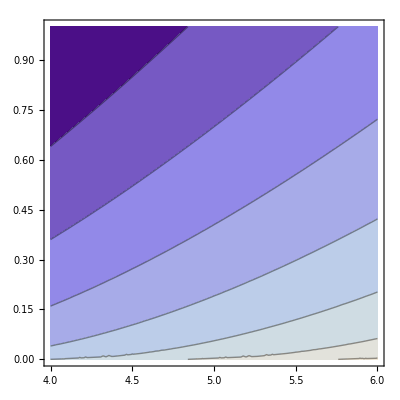

```mathematica
d1p=ContourPlot[Sqrt[x1]-Sqrt[x2],{x1,4,6},{x2,0,1}]
```

```mathematica
data=Table[{{x1,x2},{1-Sqrt[x1],Sqrt[x1] - Sqrt[x2]}},{x1,4,6,0.5},{x2,0,1,0.5}];
```

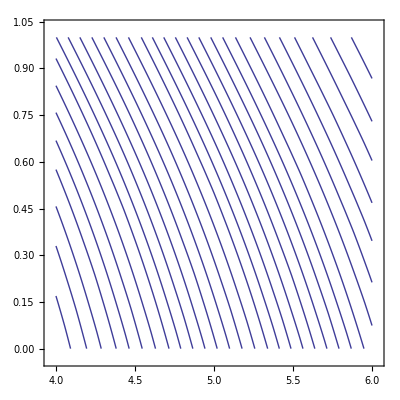

```mathematica
plot=ListStreamPlot[data,StreamStyle->"Line",PlotRangePadding->0]
```

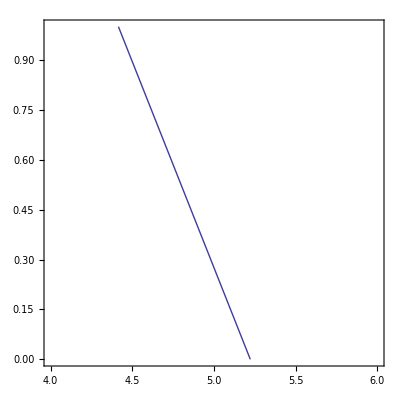

```mathematica
new=ContourPlot[x2-(6.472425572795228-1.239427818996555 x1)==0,{x1,4,6},{x2,0,1}]
```

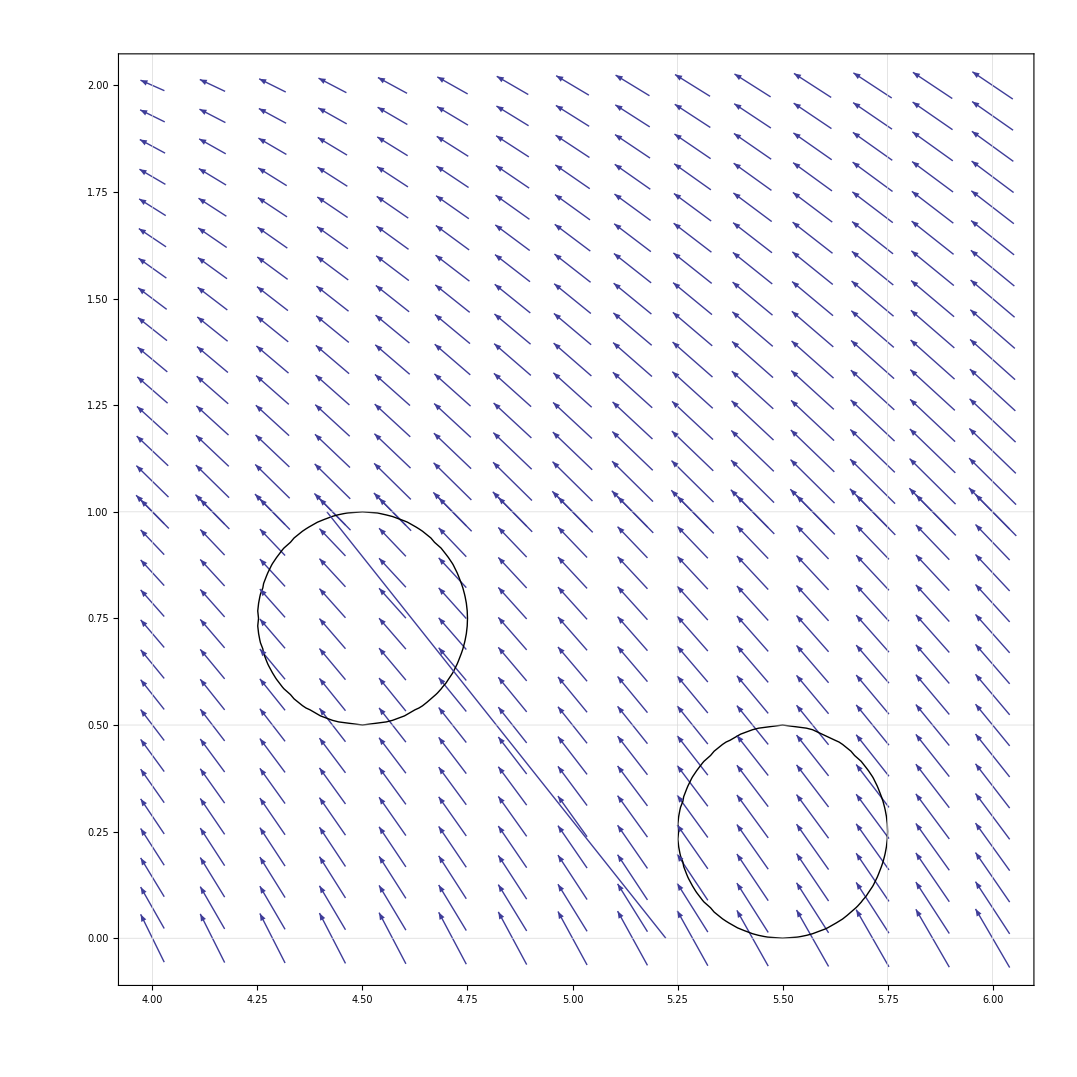

```mathematica
Show[vfs1,vfs2,bg,bg2,new,PlotRange->All]
```

```mathematica
indexes=Cases[plot,Line[index_]->index,Infinity]
```

{{118,119,120,125,126,154,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218},{220,221,222,227,228,246,247,263,264,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322},{324,325,326,331,332,356,357,358,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420},{422,423,424,429,430,439,440,441,456,457,458,459,460,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492},{494,495,496,505,506,515,516,517,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554},{556,557,558,567,568,578,579,604,605,606,607,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662},{664,665,666,675,676,684,686,687,712,713,714,715,716,717,718,719,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776},{778,779,780,785,786,799,800,801,802,803,804,805,806,807,808,809,810},{812,813,814,826,827,828,829,830,831,839,840,841,842,843,844,845,846,847,848},{850,851,852,857,858,870,871,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934},{936,937,938,950,951,952,953,954,955,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1009,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020},{1022,1023,1024,1035,1036,1037,1038,1039,1040,1081,1082,1083,1084,1085,1086,1087,1088,1089,1090,1091,1092,1093,1094,1095,1096,1097,1098,1099,1100,1101,1102,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118,1119,1120,1121,1122},{1124,1125,1126,1137,1138,1139,1140,1141,1142,1188,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1199,1200,1201,1202,1203,1204,1205,1206,1207,1208,1209,1210,1211,1212,1213,1214,1215,1216,1217,1218,1219,1220,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1233,1234},{1236,1237,1238,1248,1249,1250,1294,1295,1296,1297,1298,1299,1300,1301,1302,1303,1304,1305,1306,1307,1308,1309,1310,1311,1312,1313,1314,1315,1316,1317,1318,1319,1320,1321,1322,1323,1324,1325,1326,1327,1328,1329,1330,1331,1332,1333,1334,1335,1336,1337,1338,1339,1340},{1342,1343,1344,1354,1355,1357,1358,1359,1402,1403,1404,1405,1406,1407,1408,1409,1410,1411,1412,1413,1414,1415,1416,1417,1418,1419,1420,1421,1422,1423,1424,1425,1426,1427,1428,1429,1430,1431,1432,1433,1434,1435,1436,1437,1438,1439,1440,1441,1442,1443,1444,1445,1446},{1448,1449,1450,1454,1455,1460,1461,1462},{1464,1465,1466,1475,1476,1478,1479,1480,1481,1482},{1484,1485,1486,1490,1491,1501,1502,1503,1512,1513,1514,1515,1516,1517,1518,1519,1520,1521,1522,1523,1524},{1526,1527,1528,1536,1537,1538,1559,1560,1561,1562,1563,1564,1565,1566,1567,1568,1569,1570,1571,1572,1573,1574,1575,1576,1577,1578,1579,1580},{1582,1583,1584,1593,1594,1595,1596,1597,1598,1623,1624,1625,1626,1652,1653,1654,1655,1656,1657,1658,1659,1660,1661,1662,1663,1664,1665,1666,1667,1668,1669,1670,1671,1672,1673,1674,1675,1676,1677,1678,1679,1680,1681,1682,1683,1684,1685,1686,1687,1688,1689,1690,1691,1692,1693,1694,1695,1696},{1698,1699,1700,1704,1705,1714,1715,1716,1717,1742,1743,1744,1745,1746,1747,1748,1749,1750,1751,1752,1753,1754,1755,1756,1757,1758,1759,1760,1761,1762,1763,1764,1765,1766,1767,1768},{1770,1771,1772,1780,1781,1782,1783,1784,1785,1825,1826,1827,1828,1829,1830,1831,1832,1833,1834,1835,1836,1837,1838,1839,1840,1841,1842,1843,1844,1845,1846,1847,1848,1849,1850,1851,1852,1853,1854,1855,1856,1857,1858,1859,1860,1861,1862},{1864,1865,1866,1874,1875,1876,1877,1878,1879,1911,1912,1913,1914,1915,1916,1917,1918,1919,1920,1921,1922,1923,1924,1925,1926,1927,1928,1929,1930,1931,1932,1933,1934,1935,1936,1937,1938,1939,1940},{1942,1943,1944,1954,1955,1958,1959,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022,2023,2024,2025,2026,2027,2028,2029,2030,2031,2032,2033,2034,2035,2036,2037,2038,2039,2040,2041,2042,2043,2044},{2046,2047,2048,2055,2056,2057,2058,2059,2106,2107,2108,2109,2110,2111,2112,2113,2114,2115,2116,2117,2118,2119,2120,2121,2122,2123,2124,2125,2126,2127,2128,2129,2130,2131,2132,2133,2134,2135,2136,2137,2138,2139,2140,2141,2142,2143,2144,2145,2146,2147,2148,2149,2150},{2152,2153,2154,2162,2163,2164,2212,2213,2214,2215,2216,2217,2218,2219,2220,2221,2222,2223,2224,2225,2226,2227,2228,2229,2230,2231,2232,2233,2234,2235,2236,2237,2238,2239,2240,2241,2242,2243,2244,2245,2246,2247,2248,2249,2250,2251,2252,2253,2254,2255,2256,2257,2258,2259,2260},{2262,2263,2264,2271,2272,2273,2274,2275,2276,2324,2325,2326,2327,2328,2329,2330,2331,2332,2333,2334,2335,2336,2337,2338,2339,2340,2341,2342,2343,2344,2345,2346,2347,2348,2349,2350,2351,2352,2353,2354,2355,2356,2357,2358,2359,2360,2361,2362,2363,2364,2365,2366,2367,2368},{2370,2371,2372,2380,2381,2382,2383,2384,2431,2432,2433,2434,2435,2436,2437,2438,2439,2440,2441,2442,2443,2444,2445,2446,2447,2448,2449,2450,2451,2452,2453,2454,2455,2456,2457,2458,2459,2460,2461,2462,2463,2464,2465,2466,2467,2468,2469,2470,2471,2472,2473,2474,2475,2476},{2478,2479,2480,2487,2488,2489,2490,2491,2539,2540,2541,2542,2543,2544,2545,2546,2547,2548,2549,2550,2551,2552,2553,2554,2555,2556,2557,2558,2559,2560,2561,2562,2563,2564,2565,2566,2567,2568,2569,2570,2571,2572,2573,2574,2575,2576,2577,2578,2579,2580,2581,2582,2583,2584},{2586,2587,2588,2595,2596,2597,2642,2643,2644,2645,2646,2647,2648,2649,2650,2651,2652,2653,2654,2655,2656,2657,2658,2659,2660,2661,2662,2663,2664,2665,2666,2667,2668,2669,2670,2671,2672,2673,2674,2675,2676,2677,2678,2679,2680,2681,2682,2683,2684,2685,2686},{2688,2689,2690,2699,2700,2701,2745,2746,2747,2748,2749,2750,2751,2752,2753,2754,2755,2756,2757,2758,2759,2760,2761,2762,2763,2764,2765,2766,2767,2768,2769,2770,2771,2772,2773,2774,2775,2776,2777,2778,2779,2780,2781,2782,2783,2784,2785,2786,2787,2788,2789,2790}}

```mathematica
points=plot[[1,2,1]]
```

{{3.9656,-0.0343997},{3.9656,1.0344},{6.0344,-0.0343997},{6.0344,1.0344},{3.9656,0.0206398},{6.0344,0.0206397},{3.9656,0.0756795},{6.0344,0.0756792},{3.9656,0.130719},{6.0344,0.130719},{3.9656,0.185758},«2769»,{4.78529,0.821139},{4.76387,0.843484},{4.74254,0.865564},{4.72129,0.887397},{4.70014,0.909002},{4.67907,0.930401},{4.65809,0.951611},{4.63719,0.972642},{4.61639,0.993499},{4.60988,1.}}

```mathematica
Line[points[[indexes[[2790]]]]]
```

Line[{{3.9656,-0.0343997},{3.9656,1.0344},{6.0344,-0.0343997},{6.0344,1.0344},{3.9656,0.0206398},{6.0344,0.0206397},{3.9656,0.0756795},{6.0344,0.0756792},{3.9656,0.130719},{6.0344,0.130719},«2770»,{4.78529,0.821139},{4.76387,0.843484},{4.74254,0.865564},{4.72129,0.887397},{4.70014,0.909002},{4.67907,0.930401},{4.65809,0.951611},{4.63719,0.972642},{4.61639,0.993499},{4.60988,1.}}⟦{{118,119,«47»,217,218},«30»}⟦2790⟧⟧]

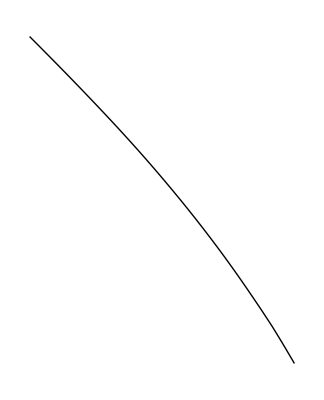

```mathematica
Show[Graphics[Line[points[[indexes[[13]]]]]]]
```

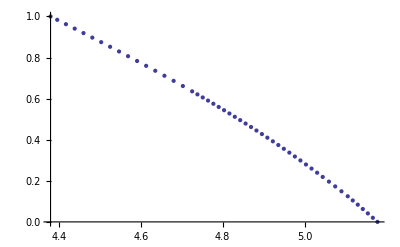

6.47243-1.23943 x

```mathematica
p=points[[indexes[[12]]]];
ListPlot[p]
Fit[p,{1,x},x]
```

```mathematica
y
```

y